```mathematica
Quit
```

f(z)=E^z

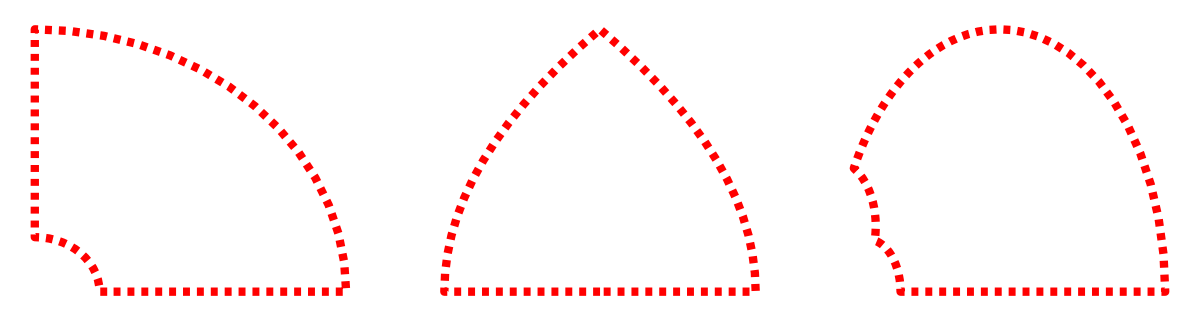

```mathematica
{fig1,fig2,fig3}=With[{z=x+I*y},ParametricPlot[ReIm[#],{x,0,1},{y,0,1},Mesh->0,MaxRecursion->2,PlotStyle->RGBColor[1,1,1,0],BoundaryStyle->Directive[Dashed,Thickness[.015],Red],Frame->False,Axes->False,PlotRange->All]]&/@{ⅇ^(1/2 π (-1+z)),1/2 z^2,1/(5-4z)};
GraphicsRow[{fig1,fig2,fig3}]
```

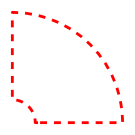

```mathematica
fig1
```

```mathematica
fig2
```

-Graphics-

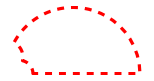

```mathematica
fig3
```

f(z)=z^2

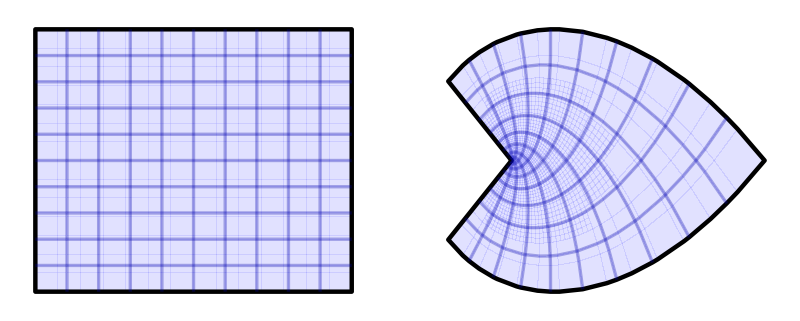

```mathematica
{fig1,fig2}=With[{z=x+I*y},ParametricPlot[ReIm[#],{x,0,1},{y,0,1},Mesh->9,MaxRecursion->2,PlotStyle->RGBColor[0.618,0.618,1],MeshStyle->Directive[Thickness[.006],Darker[Blue]],BoundaryStyle->Directive[Thickness[.008],Black],Frame->False,Axes->False]]&/@{z,-(z)^3-z^3 I};
GraphicsRow[{fig1,fig2}]
```

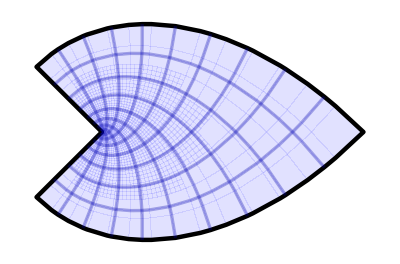

```mathematica
fig2
```